{{u[x]→1/5 ((-5+x) ArcTan[x]+2 Log[1+x^2])}}

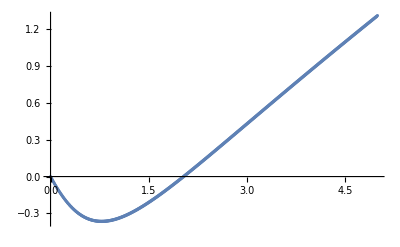

```mathematica
(* task 1*)
Clear[u, f];
implicitEuler[h_, f_, t0_, T_, u0_] := (
	n = N[Ceiling[(T-t0)/h]];
	t = Table[t0+i*h, {i, 0,n}];
	y = Table[0,{i, 0,n}];
	y[[1]] =N[u0];

	For[i=1, i ≤n, i++,
		initialGuess = y[[i]] + h*f[t[[i]],y[[i]]];
		y[[i+1]] =yNew  /. FindRoot[yNew==y[[i]]+h*(f[t[[i+1]], yNew]),
		{yNew, initialGuess}];
	];
	{t, y}
);

f[a_, b_]:=((a-1)/(a^2+1) + 1/5*ArcTan[a]);

solAppr = implicitEuler[0.01, f, 0, 5, 0];
solExact = DSolve[{u'[x]== ((x-1)/(x^2+1) + 1/5*ArcTan[x]), u[0] == 0}, u[x],{x,0,5} ]
plotExact = Plot[solExact[[1,1,2]], {x, 0, 5}];
Show[plotExact,ListPlot[Transpose[{solAppr[[1]],solAppr[[2]]}]]]
```

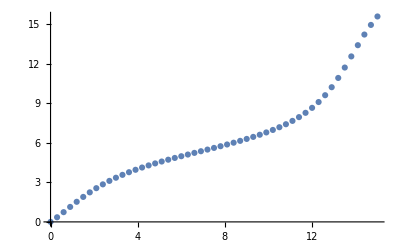

```mathematica
(*task2*)
Clear[u]
RK4[h_, f_, t0_, T_, u0_] := (
   n = N[Ceiling[(T - t0)/h]];
   t = Table[t0 + i*h, {i, 0, n}];
   y = Table[0, {i, 0, n}];
   y[[1]] = N[u0];
   
   For[i = 1, i <= n, i++,
    k1 = h*f[t[[i]], y[[i]]];
    k2 = h*f[t[[i]] + 1/2*h, y[[i]] + 1/2*k1];
    k3 = h*f[t[[i]] + 1/2*h, y[[i]] + 0*k1 + 1/2*k2];
    k4 = h*f[t[[i]] + h, y[[i]] + 0*k1 + 0*k2 + k3];
    
    y[[i+1]] = y[[i]] + 1/6*k1 + 1/3*k2 + 1/3*k3 + 1/6*k4;
   ];
   {t, y}
   );

f[t_, x_] := (Cos[x/2] + (t/4)^(1/2));
solRK4 = RK4[0.3, f, 0, 15, 0];
ListPlot[Transpose[{solRK4[[1]], Flatten[solRK4[[2]]]}]]
```